```mathematica
CellPrint[Cell["Directory","Section"]]
CellPrint[Cell["Main code & XZ independent noise:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"general_codes.nb"],Appearance->"DialogBox"]
CellPrint[Cell["DATA & code definitions :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"data_summary.nb"],Appearance->"DialogBox"]
CellPrint[Cell["Depoloarizing Noise:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"depolarizing_noise.nb"],Appearance->"DialogBox"]
CellPrint[Cell["XZ uneven Noise:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"xz_uneven_noise.nb"],Appearance->"DialogBox"]
CellPrint[Cell["Approxiating polynomials:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"approximating_polynomials.nb"],Appearance->"DialogBox"]
CellPrint[Cell["Depolarizing noise with Measurement error :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"depolarizing_noise_ME.nb"],Appearance->"DialogBox"]
CellPrint[Cell["XZ (symmetric) noise with Measurement error :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"xz_noise_ME.nb"],Appearance->"DialogBox"]
CellPrint[Cell["XZ uneven noise with Measurement error :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"xz_uneven_noise_ME.nb"],Appearance->"DialogBox"]
SetDirectory[NotebookDirectory[]]
```

## Directory

Main code & XZ independent noise:

DATA & code definitions :

Depoloarizing Noise:

XZ uneven Noise:

Approxiating polynomials:

Depolarizing noise with Measurement error :

XZ (symmetric) noise with Measurement error :

XZ uneven noise with Measurement error :

/Users/naomi/Dropbox/&Projects/Small codes

## Directory

Main code & XZ independent noise:

DATA & code definitions :

Depoloarizing Noise:

XZ uneven Noise:

Approxiating polynomials:

Depolarizing noise with Measurement error :

XZ (symmetric) noise with Measurement error :

XZ uneven noise with Measurement error :

/Users/naomi/Dropbox/&Projects/Small codes

```mathematica
countDepolarizingErrors[Q_]:=Length[Q]/2-Count[Partition[Q,2],{1,1}]


testCodeDepol[code_,testErrors_:5]:=Module[{S,L,nQubits,sLists,sVecs,sGroup,errCount,lLists,lGroup,lVecs,Qstates,syndromes},

{nQubits,S,L}=code;
(* specify the stabilizer generators, S (These should be independent operators) , and the Logical operators, L. *)

(* generate the stabilizer lists and qubit array *)
sLists = createStabilizerLists[S]; (* for measurement *)
sVecs = createStabilizerVectors[S,nQubits];(* for applying operators *)
sGroup =Times@@#&/@ Subsets[sVecs,All];

(* generate the logical operators *)
lLists = createStabilizerLists[L];
lVecs = createStabilizerVectors[L,nQubits];
lGroup=Times@@#&/@Subsets[lVecs,All];

{syndromes,Qstates}=generateSyndromes[sLists,sGroup,nQubits,testErrors];

errCount = countSyndromeErrors[#,lGroup,sGroup,countDepolarizingErrors]&/@Qstates;
{syndromes,errCount}
]



encodingPower[pVal_,polynomials_]:=Module[{poly},
successRate[pVal,polynomials]/(1-pVal)^2
]
encodingPowerDepol[pVal_,polynomials_]:=Module[{poly},
successRate[pVal,polynomials]/(1-pVal)
]
successRate[pVal_,polynomials_]:=Module[{poly},
poly=polynomials/.{p->pVal};
Plus@@(Max[#]&/@poly)
]

polynomialDepol[results_,nQ_]:=(#[[2]]*(1-p)^(nQ-#[[1]])(p/3)^#[[1]]&/@#&/@#)&/@results

plotDataDepol[results_,nQ_,function_,pRange_:{0.001,0.15,0.001}]:=Module[{polynomials},
polynomials = polynomialDepol[results,nQ];
polynomials=(Plus@@#&/@#)&/@polynomials;
Table[{p,function[p,polynomials]},{p,pRange[[1]],pRange[[2]],pRange[[3]]}]
]


plotResultsDepol[results_,nQ_,function_,color_:1,label_:None]:=Module[{polynomials,ep},
polynomials = polynomialDepol[results,nQ];
polynomials=(Plus@@#&/@#)&/@polynomials;
ep=Table[{p,function[p,polynomials]},{p,0.001,0.15,0.001}];
ListPlot[ep,Joined->True,PlotStyle->ColorData[97,color],PlotLegends->{label}]
]

checkResultsValidDepol[results_,nQ_]:=Module[{polynomials},
polynomials = (#[[2]]*(1-p)^(nQ-#[[1]])(p/3)^#[[1]]&/@#&/@#)&/@results;
polynomials=(Plus@@#&/@#)&/@polynomials;
FullSimplify[Plus@@Plus@@polynomials]
]
```

## Generate polynomials

```mathematica
testCodeDepol[codeP5]>> "data/planarDepol5.txt"
```

```mathematica
testCodeDepol[codeP6] >> "data/planarDepol6.txt"
```

```mathematica
testCodeDepol[codeP7] >> "data/planarDepol7a.txt"
```

```mathematica
testCodeDepol[codeP7b]>> "data/planarDepol7b.txt"
```

```mathematica
testCodeDepol[codeP8]>> "data/planarDepol8.txt"
```

```mathematica
testCodeDepol[codeP9]>>"data/planarDepol9.txt"
```

```mathematica
testCodeDepol[codeP13,6] >>"data/planarDepol13.txt"
```

```mathematica
testCodeDepol[codeC7]>>"data/colorDepol7.txt"
```

```mathematica
testCodeDepol[codeC9]>>"data/colorDepol9.txt"
```

```mathematica
testCodeDepol[codeC11]>>"data/colorDepol11.txt"
```

## Generate plot data

```mathematica
{syndromesT5,polyT5}=<<"data/polyXZT5.txt";
checkResultsValid[polyT5,5]
plotDataF[polyT5,5,successRate]>>"data/XZT5"
```

```mathematica
{syndromeDepolP5,polyDepolP5} =<<"data/planarDepol5.txt";
checkResultsValidDepol[polyDepolP5,5];
plotDataDepol[polyDepolP5,5,successRate]>>"data/depolS5"

{syndromeDepolP6,polyDepolP6} =<<"data/planarDepol6.txt";
checkResultsValidDepol[polyDepolP6,6];
plotDataDepol[polyDepolP6,6,successRate]>>"data/depolS6"
```

```mathematica
{syndromeDepolP7a,polyDepolP7a}=<<"data/planarDepol7a.txt";
checkResultsValidDepol[polyDepolP7a,7]
plotDataDepol[polyDepolP7a,7,successRate]>>"data/depolS7"

{syndromeDepolP7b,polyDepolP7b}=<<"data/planarDepol7b.txt";
plotDataDepol[polyDepolP7b,7,successRate]>>"data/depolS7b"

{syndromeDepolP8,polyDepolP8}=<<"data/planarDepol8.txt";
checkResultsValidDepol[polyDepolP8,8]
plotDataDepol[polyDepolP8,8,successRate]>>"data/depol8"
```

```mathematica
{syndromeDepolP9,polyDepolP9}=<<"data/planarDepol9.txt";
plotDataDepol[polyDepolP9,9,successRate]>>"data/depol9"
```

```mathematica
{syndromeDepolP13,polyDepolP13}=<<"data/planarDepol13.txt";
plotDataDepol[polyDepolP13,13,successRate]>>"data/depol13"
```

```mathematica
{syndromeDepolC7,polyDepolC7}=<<"data/colorDepol7.txt";
checkResultsValidDepol[polyDepolC7,7]
plotDataDepol[polyDepolC7,7,successRate]>>"data/depolC7"
```

1

```mathematica
{syndromeDepolC9,polyDepolC9}=<<"data/colorDepol9.txt";
checkResultsValidDepol[polyDepolC9,9]
plotDataDepol[polyDepolC9,9,successRate]>>"data/depolC9"
```

1

```mathematica
{syndromeDepolC11,polyDepolC11}=<<"data/colorDepol11.txt";
checkResultsValidDepol[polyDepolC11,11]
plotDataDepol[polyDepolC11,11,successRate]>>"data/depolC11"
```

1

```mathematica
pGCCDepol[p_]:=Module[{noError,noErrorX,e1,x1z1},

noError=(1-p)^15;
e1=15*(1-p)^14*p;
x1z1=15*14*(1-p)^13*(p/3)^2;
noError+e1+x1z1
]


Table[{p,pGCCDepol[p]},{p,0.0002,0.15,0.0002}]>> "data/depolGCC15";
```

## Summary Plots - surface codes

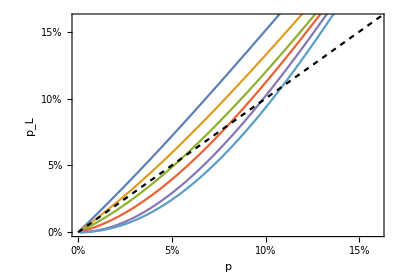

```mathematica
dataDepolP5=<<"data/depolS5";
dataDepolP6=<<"data/depolS6";
dataDepolP7=<<"data/depolS7";
dataDepolP7b=<<"data/depolS7b";
dataDepolP8=<<"data/depol8";
dataDepolP9=<<"data/depol9";

dataDepolP13=<<"data/depol13";


pLog[data_]:={#[[1]],1-#[[2]]}&/@data;


Show[ListPlot[pLog@#[[1]],Joined->True,PlotStyle->ColorData[97,#[[2]]]]&/@

{{dataDepolP5,1},{dataDepolP6,2},{dataDepolP7,3},{dataDepolP8,4},{dataDepolP9,5},{dataDepolP13,7}},

Plot[p,{p,0,1},PlotStyle->Directive[Black,Dashing[0.01]]],

Frame->True,
PlotRange->{{0,0.16},{0,0.16}},
FrameLabel->{"p","p_L"},
LabelStyle->15,
FrameTicks->{{{0,"0%"},{0.05,"5%"},{0.1,"10%"},{0.15,"15%"}},{{0,"0%"},{0.05,"5%"},{0.1,"10%"},{0.15,"15%"},{0.2,"20%"}},{},{}},
AspectRatio->0.7


]
```

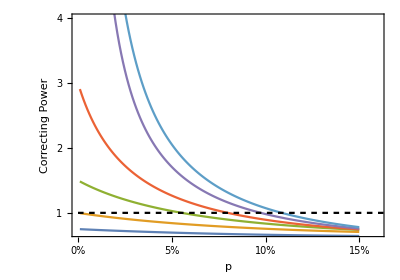

```mathematica
cp[data_]:={#[[1]],#[[1]]/(1-#[[2]])}&/@data

Show[ListPlot[cp@#[[1]],Joined->True,PlotStyle->ColorData[97,#[[2]]]]&/@

{{dataDepolP5,1},{dataDepolP6,2},{dataDepolP7,3},{dataDepolP8,4},{dataDepolP9,5},{dataDepolP13,7}},

Plot[1,{p,0,1},PlotStyle->Directive[Black,Dashing[0.01]]],

Frame->True,
PlotRange->{{0,0.16},{0.7,4}},
FrameLabel->{"p","Correcting Power"},
LabelStyle->15,
FrameTicks->{{{0,"0%"},{0.05,"5%"},{0.1,"10%"},{0.15,"15%"}},{1,2,3,4},{},{}},
AspectRatio->0.7


]
```

## Summary Plots - surface codes

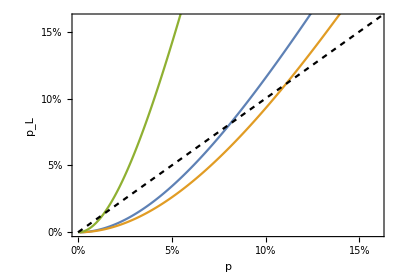

```mathematica
dataDepolC7=<<"data/depolC7";
dataDepolC9=<<"data/depolC9";
dataDepolC11=<<"data/depolC11";
dataDepolGCC15=<<"data/depolGCC15";

pLog[data_]:={#[[1]],1-#[[2]]}&/@data;


Show[ListPlot[pLog@#[[1]],Joined->True,PlotStyle->ColorData[97,#[[2]]]]&/@

{{dataDepolC7,1},{dataDepolC11,2},{dataDepolGCC15,3}},

Plot[p,{p,0,1},PlotStyle->Directive[Black,Dashing[0.01]]],

Frame->True,
PlotRange->{{0,0.16},{0,0.16}},
FrameLabel->{"p","p_L"},
LabelStyle->15,
FrameTicks->{{{0,"0%"},{0.05,"5%"},{0.1,"10%"},{0.15,"15%"}},{{0,"0%"},{0.05,"5%"},{0.1,"10%"},{0.15,"15%"},{0.2,"20%"}},{},{}},
AspectRatio->0.7


]
```

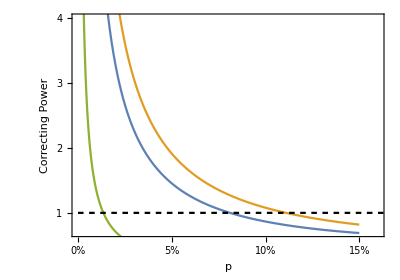

```mathematica
Show[ListPlot[cp@#[[1]],Joined->True,PlotStyle->ColorData[97,#[[2]]]]&/@

{{dataDepolC7,1},{dataDepolC11,2},{dataDepolGCC15,3}},

Plot[1,{p,0,1},PlotStyle->Directive[Black,Dashing[0.01]]],

Frame->True,
PlotRange->{{0,0.16},{0.7,4}},
FrameLabel->{"p","Correcting Power"},
LabelStyle->15,
FrameTicks->{{{0,"0%"},{0.05,"5%"},{0.1,"10%"},{0.15,"15%"}},{1,2,3,4},{},{}},
AspectRatio->0.7


]
```

## 5 qubit planar

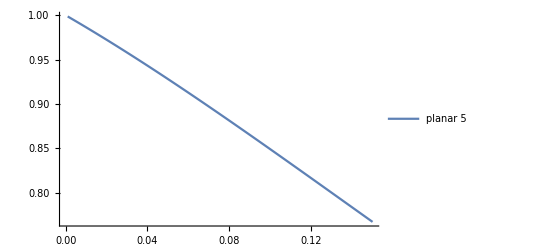
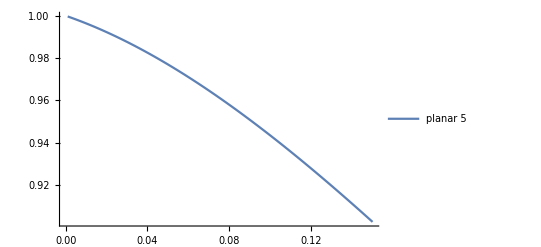

```mathematica
{plotPlanarDepol5,epPlanarDepol5}={plotResultsDepol[polyDepolP5,5,successRate,1,"planar 5"],
plotResultsDepol[polyDepolP5,5,encodingPowerDepol,1,"planar 5"]}
```

## 6 qubit planar

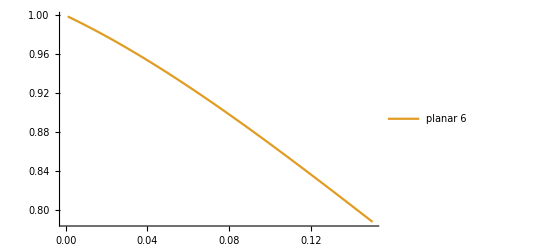
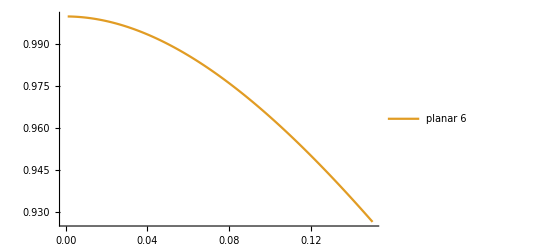

```mathematica
{plotPlanarDepol6,epPlanarDepol6}={plotResultsDepol[polyDepolP6,6,successRate,2,"planar 6"],
plotResultsDepol[polyDepolP6,6,encodingPowerDepol,2,"planar 6"]}
```

## 7 qubit Planar Codes

1

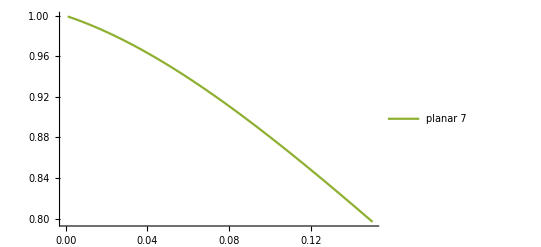
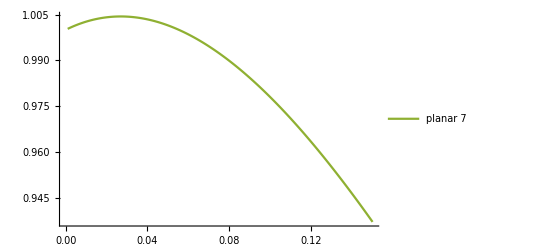

```mathematica
{plotPlanarDepol7a,epPlanarDepol7a}={plotResultsDepol[polyDepolP7a,7,successRate,3,"planar 7"],
plotResultsDepol[polyDepolP7a,7,encodingPowerDepol,3,"planar 7"]}
```

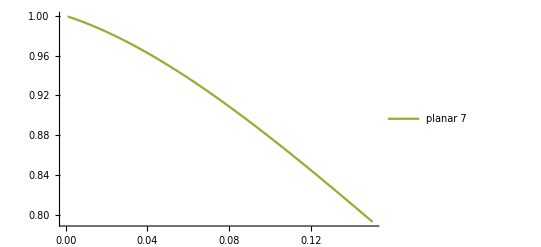
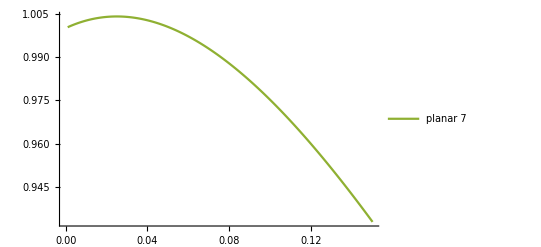

```mathematica
{plotPlanarDepol7b,epPlanarDepol7b}={plotResultsDepol[polyDepolP7b,7,successRate,3,"planar 7"],
plotResultsDepol[polyDepolP7b,7,encodingPowerDepol,3,"planar 7"]}
```

## 8 qubit surface Code

1

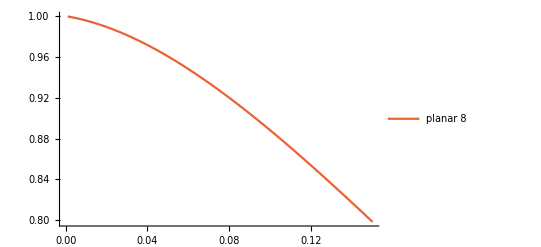
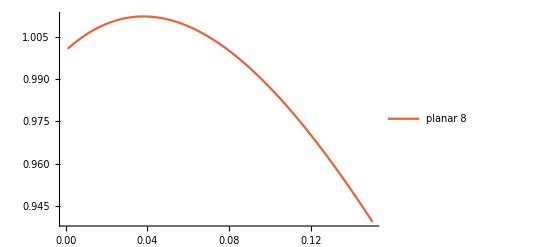

```mathematica
{plotPlanarDepol8,epPlanarDepol8}={plotResultsDepol[polyDepolP8,8,successRate,4,"planar 8"],plotResultsDepol[polyDepolP8,8,encodingPowerDepol,4,"planar 8"]}
```

## 9 qubit surface Code

```mathematica
plotPlanarDepol9=plotResultsDepol[polyDepolP9,9,successRate,5,"planar 9"]
epPlanarDepol9=plotResultsDepol[polyDepolP9,9,encodingPowerDepol,5,"planar 9"]
```

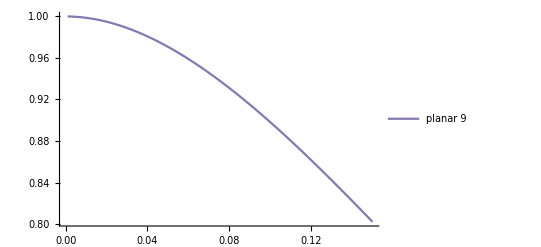
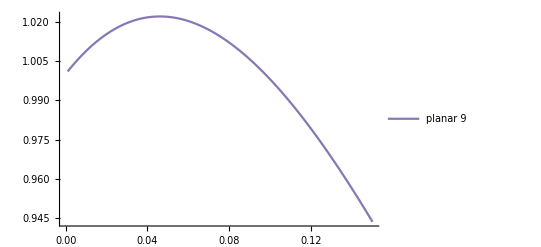

## 13 qubit surface Code

```mathematica
plotPlanarDepol13=plotResultsDepol[polyDepolP13,13,successRate,5,"planar 9"]
```

$Aborted

## 7 qubit Color Code

1

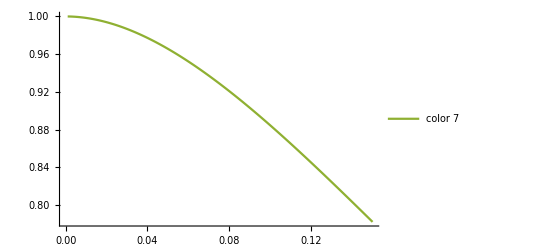

```mathematica
{plotColorDepol7}={plotResultsDepol[polyDepolC7,7,successRate,3,"color 7"]}
```

## 9 qubit Color Code

1

1

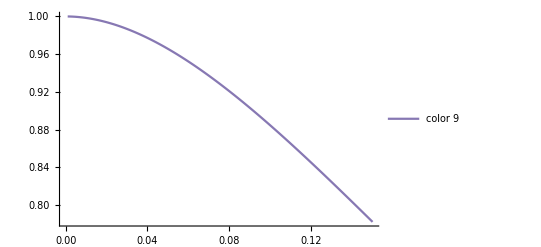

```mathematica
{plotColorDepol9}={plotResultsDepol[polyDepolC9,9,successRate,5,"color 9"]}
```

## 11 qubit Color Code

```mathematica
plotDataDepol[polyDepolC11,11,successRate,{0.001,0.25,0.01}]>>"data/plotdataDepolC11"
```

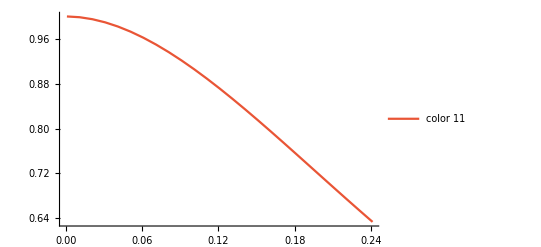

```mathematica
plotDataDepolC11=<<"data/plotdataDepolC11";
{plotColorDepol11}={ListPlot[plotDataDepolC11,Joined->True,PlotStyle->ColorData[97,11],PlotLegends->{"color 11"}]}
```

## Comparison of codes

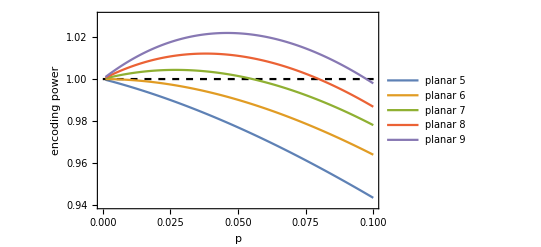

```mathematica
Show[
epPlanarDepol5,ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],epPlanarDepol6,epPlanarDepol7,epPlanarDepol8,epPlanarDepol9,
PlotRange->{{0,0.1},{0.94,1.03}},Frame->True,FrameLabel->{"p","encoding power"},LabelStyle->Medium]
```

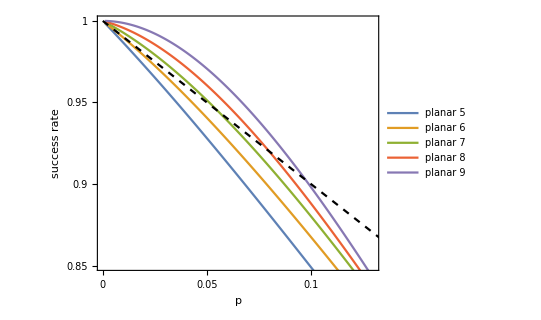

```mathematica
Show[plotPlanarDepol5,plotPlanarDepol6,plotPlanarDepol7,plotPlanarDepol8,plotPlanarDepol9,
Plot[(1-p),{p,0,1},PlotStyle->{Black,Dashed}],

PlotRange->{{0,0.13},{0.85,1}},Frame->True,FrameLabel->{"p","success rate"},LabelStyle->20,FrameTicks->{{{0.8,0.85,0.9,0.95,1},None},{{0,0.05,0.1,0.15},None}},AspectRatio->0.8]
```

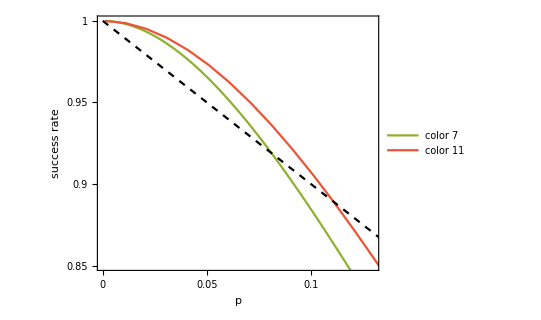

```mathematica
Show[plotColorDepol7,plotColorDepol11,
Plot[(1-p),{p,0,1},PlotStyle->{Black,Dashed}],

PlotRange->{{0,0.13},{0.85,1}},Frame->True,FrameLabel->{"p","success rate"},LabelStyle->20,FrameTicks->{{{0.8,0.85,0.9,0.95,1},None},{{0,0.05,0.1,0.15},None}},AspectRatio->0.8]
```